```mathematica
Clear["Global`*"];Off[General::spell1]
```

Feb 21 2014
martin.pos@nxp.com

```mathematica
l=RandomReal[{0,1},{1000}];
```

```mathematica
Length[l]
```

1000

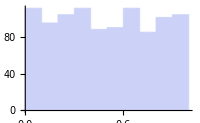

```mathematica
Histogram[l,10, ImageSize -> 200]
```

```mathematica
??Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True.

Attributes[Select]={Protected}

```mathematica
??Split
```

Split[list] splits list into sublists consisting of runs of identical elements. 
Split[list,test] treats pairs of adjacent elements as identical whenever applying the function test to them yields True.

Attributes[Split]={Protected}

```mathematica
/@
```